```mathematica
Práctica IV
```

```mathematica
Definiciones:
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);sy=(sp-sm)/(I);s1[1]=sx;s1[2]=sy;s1[3]=sz;s1[4]={{1,0},{0,1}};s1[i_,j_]=KroneckerProduct[s1[i],s1[j]];
s={sx,sy,sz};
fs=FullSimplify;
mf=MatrixForm;
prod=KroneckerProduct;
id=IdentityMatrix;
mf=MatrixForm;
T=Transpose;
daga=ConjugateTranspose;

(* Transpuesta parcial General *)
Clear[nu,nn,au,i,j];
ind[nu_,nn_]:={iaux=1+Floor[(nu-1)/nn],nu-(iaux-1)*nn};
rhotp[au_]:=(nn=Sqrt[Length[au]];
Table[{i,j}=ind[it,nn];{k,l}=ind[jt,nn];
au[[nn*(i-1)+l,nn*(k-1)+j]],{it,nn^2},{jt,nn^2}]); 

(* Base Estándar *)

st0={1,0};st1={0,1};
stp=(st0+st1)/√2;
stm=(st0-st1)/√2;
st00=Flatten[prod[st0,st0]];
st01=Flatten[prod[st0,st1]];
st10=Flatten[prod[st1,st0]];
st11=Flatten[prod[st1,st1]];

(* Proyectores en la Base Estándar *)

P0={{1,0},{0,0}};
P1={{0,0},{0,1}};

n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2];
σ={s1[1],s1[2],s1[3]};

(* Rotación General de un qubit *)

R[i_,θ_]=MatrixExp[-I θ n[i].σ/2] ;
```

```mathematica
PacletInstall["/home/alan/Documentos/SeminarioCuantica/MaTeX-1.7.7.paclet"]
```

Paclet[MaTeX,1.7.7,<>]

```mathematica
<<MaTeX`
```

## I. Evoluci ́on de sistemas cu ́anticos abiertos

#### Problema 2

```mathematica
a) Mostrar que para el caso de la evoluci ́on por un operador control not
 UAB=|0〉〈0|⊗I+|1〉〈1|⊗X
de un estado producto de dos qubits
ρAB=ρA⊗|ψB〉〈ψB|,
se obtiene
ρ′A=(1−p)ρA+pZρAZ
Dar el valor expĺıcito depe identificar los operadores E0 y E1.
```

```mathematica
Unot=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}})
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
stp
```

{1/(√2),1/(√2)}

```mathematica
ArrayReshape[Unot,{2,2,2,2}]
```

{{{{1,0},{0,0}},{{0,1},{0,0}}},{{{0,0},{0,1}},{{0,0},{1,0}}}}

```mathematica
PsiB=c1 stp + c2 stm;
```

```mathematica
E0=stp.ArrayReshape[Unot,{2,2,2,2}].Conjugate[stp]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
e[1]={{α,0},{0,β}};
e[2]={{β,0},{0,α}};
ρA=prod[{γ,δ},Conjugate[{γ,δ}]];
ρAev=e[1].ρA.ConjugateTranspose[e[1]]+e[2].ρA.ConjugateTranspose[e[2]]//fs;
ρAev=%/. Abs[α]^2+Abs[β]^2-> 1;
Print[ρAev//fs//mf](*matriz densidad en A luego de la evolucion*)
Solve[{ρAev== (1-p)ρA+p σz.ρA.σz},p]
```

(Abs[γ]^2 | γ (β Conjugate[α]+α Conjugate[β]) Conjugate[δ]
δ (β Conjugate[α]+α Conjugate[β]) Conjugate[γ] | Abs[δ]^2)

{}

```mathematica
ρAev
```

{{γ Conjugate[γ],γ (β Conjugate[α]+α Conjugate[β]) Conjugate[δ]},{δ (β Conjugate[α]+α Conjugate[β]) Conjugate[γ],δ Conjugate[δ]}}

```mathematica
E0=c1({{1, 0}, {0, 1}});E1=c2({{1, 0}, {0, -1}});
```

```mathematica
rhoA=prod[{a,b},Conjugate[{a,b}]];
```

```mathematica
c1=√(1-p);c2=√p;
```

```mathematica
rhoAEv=E0.rhoA.Transpose[E0]+E1.rhoA.Transpose[E1]
```

{{a (1-p) Conjugate[a]+a p Conjugate[a],a (1-p) Conjugate[b]-a p Conjugate[b]},{b (1-p) Conjugate[a]-b p Conjugate[a],b (1-p) Conjugate[b]+b p Conjugate[b]}}

```mathematica
Assuming[Abs[a]^2+Abs[b]^2->1,FullSimplify[1/2 (Abs[a]^2+Abs[b]^2-√(Abs[a]^4+Abs[b]^4+2 a b (1+8 (-1+p) p) Conjugate[a] Conjugate[b]))]]
```

1/2 (Abs[a]^2+Abs[b]^2-√(Abs[a]^4+Abs[b]^4+2 a b (1+8 (-1+p) p) Conjugate[a] Conjugate[b]))

```mathematica
b=√(Abs[a]^2-1)
```

√(-1+Abs[a]^2)

```mathematica
Eigenvalues[rhoAEv]//fs
```

{1/2 (Abs[a]^2+Abs[-1+Abs[a]^2]-√(1+2 Abs[a]^4+2 a (-1+(1+8 (-1+p) p) Abs[-1+Abs[a]^2]) Conjugate[a])),1/2 (Abs[a]^2+Abs[-1+Abs[a]^2]+√(1+2 Abs[a]^4+2 a (-1+(1+8 (-1+p) p) Abs[-1+Abs[a]^2]) Conjugate[a]))}

```mathematica
rhoAevol=({{Cos[th]^2, (1-2 p) Sin[th] Cos[th]}, {(1-2 p) Sin[th] Cos[th], Sin[th]^2}});
```

```mathematica
{λ1,λ2}=Eigenvalues[rhoAevol]//fs
```

{1/2 (1-√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th])),1/2 (1+√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th]))}

```mathematica
Ent[p_,th_]:=-λ1 Log2[λ1]-λ2 Log2[λ2]
```

```mathematica
Ent[p_,th_]:=((-1+√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th])) Log[1/2 (1-√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th]))])/(2 Log[2])-((1+√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th])) Log[1/2 (1+√(1+2 (-1+p) p-2 (-1+p) p Cos[4 th]))])/(2 Log[2])
```

```mathematica
ListAnimate[Table[Plot[Ent[p,th],{th,0,Pi/2},Frame->True,
FrameLabel->{"θ","E[ρ_AB]"},
GridLines->{{Pi/4},{}},
FrameStyle->Directive[Black,16],PlotRange->{{0,1.54},{0,1.1}}],{p,0,1,.01}],AnimationRunning->False]
```

```mathematica
b) si el sistema B se describe por Subscript[ρ, B]=∑Subscript[q, l]|l\\l| se tienen 4 operadores
```

```mathematica
(* E00=√q0 P0;E01=√q1 P1;E10=√q0 P1;E11=√q1 P0; si fuera diagonal en la base estandar pero en general hay que considerar bases primadas *)
```

```mathematica
(* q0+q1=1 *)
```

```mathematica
E00=√q0 P0;E01=√(1-q0)P1;E10=√q0 P1;E11=√(1-q0)P0;
```

```mathematica
rhoAEvolu=E00.rhoA.Transpose[E00]+E01.rhoA.Transpose[E01]+E10.rhoA.Transpose[E10]+
E11.rhoA.Transpose[E11]//fs
```

```mathematica
{{Abs[a]^2,0},{0,Abs[-1+Abs[a]^2]}}
```

```mathematica
(* Como se pensó diagonal en la base estándar se tiene decoherencia máxima, más adelante se ve que en general depende de rx=Tr[Subscript[ρ, B] Subscript[σ, X]] que en este caso es 0 *)
```

```mathematica
Tr[(q0 prod[st0,st0]+(1-q0) prod[st1,st1]).s1[1]]//fs
```

0

```mathematica
(* Tomando traza a partir de la evolución con Unot *)

rhoB=prod[{a2,b2},Conjugate[{a2,b2}]] (* con rhoB puro *)
```

{{a2 Conjugate[a2],a2 Conjugate[b2]},{b2 Conjugate[a2],b2 Conjugate[b2]}}

```mathematica
rhoA
```

{{a Conjugate[a],a Conjugate[√(-1+Abs[a]^2)]},{√(-1+Abs[a]^2) Conjugate[a],√(-1+Abs[a]^2) Conjugate[√(-1+Abs[a]^2)]}}

```mathematica
Map[Tr,Partition[Unot.prod[rhoA,rhoB].daga[Unot],{2,2}],{2}]//fs
```

{{a (Abs[a2]^2+Abs[b2]^2) Conjugate[a],a (b2 Conjugate[a2]+a2 Conjugate[b2]) Conjugate[√(-1+Abs[a]^2)]},{√(-1+Abs[a]^2) Conjugate[a] (b2 Conjugate[a2]+a2 Conjugate[b2]),(Abs[a2]^2+Abs[b2]^2) Abs[-1+Abs[a]^2]}}

```mathematica
{{Abs[a]^2,a (b2 Conjugate[a2]+a2 Conjugate[b2]) Conjugate[√(-1+Abs[a]^2)]},{√(-1+Abs[a]^2) Conjugate[a] (b2 Conjugate[a2]+a2 Conjugate[b2]), Abs[-1+Abs[a]^2]}}
```

```mathematica
(* b2 Conjugate[a2]+a2 Conjugate[b2]=1-2p *)
```

b2 Conjugate[a2]+a2 Conjugate[b2]

```mathematica
rhoB
```

{{a2 Conjugate[a2],a2 Conjugate[b2]},{b2 Conjugate[a2],b2 Conjugate[b2]}}

```mathematica
si es I a2 Conjugate[b2]=b2 Conjugate[a2]=0 entonces p=1/2, decoherencia completa
```

```mathematica
(* Otra forma es sacar operadores de Kraus generales a partir de un rhoB diagonal en una base primada
rhoB=q0 prod[stB0,stB0]+(1-q0) prod[stB1,stB1]  *)
```

```mathematica
UB=({{Cos[th], Sin[th]}, {-Sin[th], Cos[th]}});
```

```mathematica
UB.Transpose[UB]//fs
```

{{1,0},{0,1}}

```mathematica
({{stB0}, {stB1}})=UB.({{st0}, {st1}})
```

{{{Cos[th],Sin[th]}},{{-Sin[th],Cos[th]}}}

```mathematica
stB0.stB0
```

Cos[th]^2+Sin[th]^2

```mathematica
E0stB0=√q0(P0 st0.stB0 + P1 st0.s1[1].stB0)
```

{{√q0 Cos[th],0},{0,√q0 Sin[th]}}

```mathematica
E0stB1=√(1-q0)(P0 st0.stB1 + P1 st0.s1[1].stB1)

E1stB0=√q0(P0 st1.stB0 + P1 st1.s1[1].stB0)

E1stB1=√(1-q0)(P0 st1.stB1 + P1 st1.s1[1].stB1)
```

{{-√(1-q0) Sin[th],0},{0,√(1-q0) Cos[th]}}

{{√q0 Sin[th],0},{0,√q0 Cos[th]}}

{{√(1-q0) Cos[th],0},{0,-√(1-q0) Sin[th]}}

```mathematica
rhoAEvolucion=E0stB0.rhoA.Transpose[E0stB0]+E0stB1.rhoA.Transpose[E0stB1]+E1stB0.rhoA.Transpose[E1stB0]+
E1stB1.rhoA.Transpose[E1stB1]//fs
```

{{Abs[a]^2,a (-1+2 q0) Conjugate[b] Sin[2 th]},{b (-1+2 q0) Conjugate[a] Sin[2 th],Abs[b]^2}}

```mathematica
s1[1].stB0
```

{Sin[th],Cos[th]}

```mathematica
s1[1].stB1
```

{Cos[th],-Sin[th]}

```mathematica
stB0.s1[1].stB0+stB1.s1[1].stB1
```

```mathematica
Tr[(q0 prod[stB0,stB0]+(1-q0) prod[stB1,stB1]).s1[1]]//fs
```

(-1+2 q0) Sin[2 th]

```mathematica
prod[stB0,stB1]
```

{{-Cos[th] Sin[th],Cos[th]^2},{-Sin[th]^2,Cos[th] Sin[th]}}

```mathematica
(* Cuando q0=1/2 rhoB=I se recupera decoherencia máxima *)
```

```mathematica
(* rhoB=(Sum[r[[i]]s1[i],{i,1,4}])/2 
r={rx,ry,rz,1} *)

r={rx,ry,rz,1};
(Sum[r[[i]]s1[i],{i,1,4}])/2
```

{{(1+rz)/2,1/2 (rx-ⅈ ry)},{1/2 (rx+ⅈ ry),(1-rz)/2}}

```mathematica
(* en general es una matriz hermítica de Traza 1, b1=(1+rz)/2;b2=1/2 (rx-ⅈ ry) *)
```

```mathematica
rhoBg=({{b1, b2}, {Conjugate[b2], 1-b1}});
```

```mathematica
Map[Tr,Partition[Unot.prod[rhoA,rhoBg].daga[Unot],{2,2}],{2}]//fs
```

{{Abs[a]^2,2 a Conjugate[b] Re[b2]},{2 b Conjugate[a] Re[b2],Abs[b]^2}}

```mathematica
(* b2=1/2 (rx-ⅈ ry), por lo que 2 Re[b2]=rx=Tr[Subscript[ρ, B] Subscript[σ, X]] *)
```

#### Problema 3

```mathematica
Clear[e];
e[1]={{1,0},{0,0}}+√(1-p){{0,0},{0,1}};
e[2]=√p{{0,1},{0,0}};
T[e[1]].e[1]+T[e[2]].e[2]//fs;(*id[2]*)
e[1].T[e[1]]+e[2].T[e[2]]//fs;
ρA=prod[{γ,δ},Conjugate[{γ,δ}]](*ρA puro*)
ρAev=e[1].ρA.T[e[1]]+e[2].ρA.T[e[2]];
Print[ρAev//fs//mf]
```

{{γ Conjugate[γ],γ Conjugate[δ]},{δ Conjugate[γ],δ Conjugate[δ]}}

(Abs[γ]^2+p δ Conjugate[δ] | √(1-p) γ Conjugate[δ]
√(1-p) δ Conjugate[γ] | -(-1+p) δ Conjugate[δ])

```mathematica
T[e[1]].e[1]+T[e[2]].e[2]//fs
```

{{1,0},{0,1}}

```mathematica
(*id[2]*)
e[1].T[e[1]]+e[2].T[e[2]]//fs
```

{{1+p,0},{0,1-p}}

```mathematica
b)
```

```mathematica
ρA=prod[{γ,δ},Conjugate[{γ,δ}]](*ρA puro*)
ρAev=e[1].ρA.T[e[1]]+e[2].ρA.T[e[2]]
```

{{γ Conjugate[γ],γ Conjugate[δ]},{δ Conjugate[γ],δ Conjugate[δ]}}

{{γ Conjugate[γ]+p δ Conjugate[δ],√(1-p) γ Conjugate[δ]},{√(1-p) δ Conjugate[γ],(1-p) δ Conjugate[δ]}}

```mathematica
ρAth=prod[{Cos[th],Sin[th]},{Cos[th],Sin[th]}](*ρA puro*)
ρAevth=e[1].ρAth.T[e[1]]+e[2].ρAth.T[e[2]]
```

{{Cos[th]^2,Cos[th] Sin[th]},{Cos[th] Sin[th],Sin[th]^2}}

{{Cos[th]^2+p Sin[th]^2,√(1-p) Cos[th] Sin[th]},{√(1-p) Cos[th] Sin[th],(1-p) Sin[th]^2}}

```mathematica
{λth1,λth2}=Eigenvalues[ρAevth]
```

{1/4 (2-√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th])),1/4 (2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th]))}

```mathematica
-λth1 Log2[λth1]-λth2 Log2[λth2]
```

1/(4 Log[2])(-2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th])) Log[1/4 (2-√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th]))]-1/(4 Log[2])(2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th])) Log[1/4 (2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th]))]

```mathematica
Enth[p_,th_]:=1/(4 Log[2])(-2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th])) Log[1/4 (2-√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th]))]-1/(4 Log[2])(2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th])) Log[1/4 (2+√2 √(2-3 p+3 p^2+4 p Cos[2 th]-4 p^2 Cos[2 th]-p Cos[4 th]+p^2 Cos[4 th]))]
```

```mathematica
Clear[p]
```

```mathematica
ListAnimate[Table[Plot[Enth[p,th],{th,0,Pi},Frame->True,
FrameLabel->{"θ","E[ρ_AB]"},
GridLines->{{Pi/2},{}},
FrameStyle->Directive[Black,16],PlotRange->{{0,3.154},{0,1.1}}],{p,0,1,.01}],AnimationRunning->False]
```

```mathematica
(* Para un rhoA general *)
```

```mathematica
rhoAg=({{a1, a2}, {Conjugate[a2], 1-a1}});
```

```mathematica
rhoAgEv=e[1].rhoAg.T[e[1]]+e[2].rhoAg.T[e[2]]//fs
```

{{a1+p-a1 p,a2 √(1-p)},{√(1-p) Conjugate[a2],(-1+a1) (-1+p)}}

```mathematica
{la1,la2}=Eigenvalues[rhoAgEv]//fs
```

{1/2 (1-√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2])),1/2 (1+√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2]))}

```mathematica
Entg[p_,a1_,a2_]:=la1 Log2[la1]-la2 Log2[la2]
```

```mathematica
Entg[p,a1,a2]
```

1/(2 Log[2])(1-√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2])) Log[1/2 (1-√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2]))]-1/(2 Log[2])(1+√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2])) Log[1/2 (1+√((1+2 a1 (-1+p)-2 p)^2-4 a2 (-1+p) Conjugate[a2]))]

```mathematica
(* Chequeo si rhoA es puro se recupera el resultado anterior *)
```

```mathematica
a1=Cos[th]^2 ;
a2=Cos[th] Sin[th];
```

```mathematica
Entg[p,a1,a2]
```

1/(2 Log[2])Log[1/2 (1-√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))] (1-√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))-1/(2 Log[2])Log[1/2 (1+√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))] (1+√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))

```mathematica
Entgth[p_,th_]:=1/(2 Log[2])Log[1/2 (1-√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))] (1-√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))-1/(2 Log[2])Log[1/2 (1+√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))] (1+√((1-2 p+2 (-1+p) Cos[th]^2)^2-4 (-1+p) Conjugate[Cos[th] Sin[th]] Cos[th] Sin[th]))
```

```mathematica
Enth[p,th];
```

```mathematica
ListAnimate[Table[Plot[Enth[p,th],{th,0,Pi},Frame->True,
FrameLabel->{"θ","E[ρ_AB]"},
GridLines->{{Pi/2},{}},
FrameStyle->Directive[Black,16],PlotRange->{{0,3.154},{0,1.1}}],{p,0,1,.01}],AnimationRunning->False]
```

### Problema 4:

```mathematica
Clear[rhoA];
```

```mathematica
(*Estado inicial, ground state del atomo y vacio de fotones, no pasa nada*)
fs=FullSimplify;mf=MatrixForm;
Clear[e,p0,p1]
e[0][0]=√p0{{1,0},{0,Cos[θ]}};
e[0][1]=√p1{{0,0},{-Sin[θ],0}};
e[1][0]=√p0{{0,Sin[θ]},{0,0}};
e[1][1]=√p1{{Cos[θ],0},{0,1}};
Print["E_(00=)",mf[e[0][0]],"   E_(01=)",mf[e[0][1]],"   E_(10=)",mf[e[1][0]],"   E_(11=)",mf[e[1][1]]]
rhoA0=KroneckerProduct[{1,0},{1,0}];(*Estado inicial ground state*)
p1=0;p0=1;
rhoA0ev=e[0][0].rhoA0.Transpose[e[0][0]]+e[1][0].rhoA0.Transpose[e[1][0]]//fs;
Print["ρ_inicial=",mf[rhoA0],"    ρ_evolucionado",rhoA0ev//mf]
Clear[p1,p0]
```

E_(00=)(√p0 | 0
0 | √p0 Cos[θ])   E_(01=)(0 | 0
-√p1 Sin[θ] | 0)   E_(10=)(0 | √p0 Sin[θ]
0 | 0)   E_(11=)(√p1 Cos[θ] | 0
0 | √p1)

ρ_inicial=(1 | 0
0 | 0)    ρ_evolucionado(1 | 0
0 | 0)

```mathematica
(*Vacio de fotones + probabilidad de desexcitacion*)
Clear[e,p0,p1]
e[0]={{1,0},{0,Cos[θ]}};
e[1]={{0,Sin[θ]},{0,0}};

(*estado inicial, combinacion lineal*)
rhoA=p0 KroneckerProduct[{1,0},{1,0}] + (1-p0) KroneckerProduct[{0,1},{0,1}];
rhoAev=e[0].rhoA.Transpose[e[0]]+e[1].rhoA.Transpose[e[1]]//fs;
Print["ρ_inicial=",mf[rhoA],"    ρ_evolucionado",rhoAev//mf]
```

ρ_inicial=(p0 | 0
0 | 1-p0)    ρ_evolucionado(p0-(-1+p0) Sin[θ]^2 | 0
0 | -(-1+p0) Cos[θ]^2)

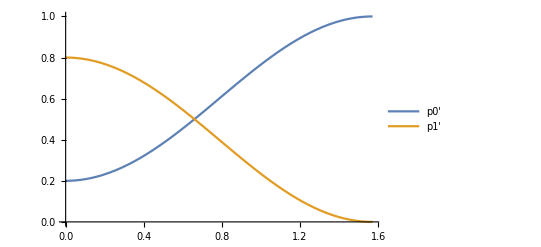

```mathematica
p0=0.2;
Plot[{p0-(-1+p0) Sin[θ]^2,-(-1+p0) Cos[θ]^2},{θ,0,π/2},FrameLabel->{"θ",""},FrameStyle->Directive[Black,16],PlotLegends->{"p0'","p1'"}]
```

```mathematica
(* rhoAev a partir de tomar traza de la evolución unitaria UAC *)
```

```mathematica
UAC=({{1, 0, 0, 0}, {0, Cos[th], Sin[th], 0}, {0, -Sin[th], Cos[th], 0}, {0, 0, 0, 1}})
```

{{1,0,0,0},{0,Cos[th],Sin[th],0},{0,-Sin[th],Cos[th],0},{0,0,0,1}}

```mathematica
(* Estado inicial conjunto *)

rhoAC=prod[rhoA,P0]
```

{{p0,0,0,0},{0,0,0,0},{0,0,1-p0,0},{0,0,0,0}}

```mathematica
(* Se obtiene el mismo Estado evolucionado de A *)
```

```mathematica
Map[Tr,Partition[UAC.rhoAC.daga[UAC],{2,2}],{2}]
```

{{p0+(1-p0) Conjugate[Sin[th]] Sin[th],0},{0,(1-p0) Conjugate[Cos[th]] Cos[th]}}

```mathematica
rhoAev
```

{{p0-(-1+p0) Sin[θ]^2,0},{0,-(-1+p0) Cos[θ]^2}}

```mathematica
(* Determinar también un Subscript[H, AC] y un tiempo t tal que exp[−iH AC t]=U AC. *)
```

```mathematica
Subscript[H, AC]=Δϵ (prod[st10,st10]+prod[st01,st01])+(g/2)(prod[st01,st10]+prod[st10,st01])
```

{{0,0,0,0},{0,Δϵ,g/2,0},{0,g/2,Δϵ,0},{0,0,0,0}}

```mathematica
MatrixExp[-I Subscript[H, AC] t]//fs
```

{{1,0,0,0},{0,ⅇ^(-ⅈ t Δϵ) Cos[(g t)/2],-ⅈ ⅇ^(-ⅈ t Δϵ) Sin[(g t)/2],0},{0,-ⅈ ⅇ^(-ⅈ t Δϵ) Sin[(g t)/2],ⅇ^(-ⅈ t Δϵ) Cos[(g t)/2],0},{0,0,0,1}}

```mathematica
UAC
```

{{1,0,0,0},{0,Cos[th],Sin[th],0},{0,-Sin[th],Cos[th],0},{0,0,0,1}}

```mathematica
Solve[ⅇ^(-ⅈ t Δϵ) Cos[(g t)/2]==Cos[th],t]
```

```mathematica
(* Si t Δϵ=2kπ y gt/2=th, se recupera UAC *)
```

```mathematica
(* Para realizarlo a través del circuito *)
```

```mathematica
stA=al st0 +be st1;
```

```mathematica
Ry=({{Cos[ga], -Sin[ga]}, {Sin[ga], Cos[ga]}});
```

```mathematica
(* B empieza en st0 y se le aplica Ry *)
```

```mathematica
(*Control-Ry *)
```

```mathematica
s1[4]
```

{{1,0},{0,1}}

```mathematica
UconRy=prod[P0,s1[4]]+prod[P1,Ry]
```

{{1,0,0,0},{0,1,0,0},{0,0,Cos[ga],-Sin[ga]},{0,0,Sin[ga],Cos[ga]}}

```mathematica
stAB=Flatten[prod[stA,st0]]
```

{al,0,be,0}

```mathematica
UconRy.stAB
```

{al,0,be Cos[ga],be Sin[ga]}

```mathematica
(* Se aplica el Control invertido I⊗P0+X⊗P1 *)
```

```mathematica
Uinv=prod[s1[4],P0]+prod[s1[1],P1]
```

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

```mathematica
Uinv.st11
```

{0,1,0,0}

```mathematica
stABf=Uinv.UconRy.stAB
```

{al,be Sin[ga],be Cos[ga],0}

```mathematica
prod[stABf,Conjugate[stABf]]//fs
```

{{Abs[al]^2,al Conjugate[be] Sin[Conjugate[ga]],al Conjugate[be] Cos[Conjugate[ga]],0},{be Conjugate[al] Sin[ga],be Conjugate[be] Sin[ga] Sin[Conjugate[ga]],be Conjugate[be] Cos[Conjugate[ga]] Sin[ga],0},{be Conjugate[al] Cos[ga],be Conjugate[be] Cos[ga] Sin[Conjugate[ga]],be Conjugate[be] Cos[ga] Cos[Conjugate[ga]],0},{0,0,0,0}}

```mathematica
Map[Tr,Partition[prod[stABf,Conjugate[stABf]],{2,2}],{2}]
```

{{al Conjugate[al]+be Conjugate[be Sin[ga]] Sin[ga],al Conjugate[be Cos[ga]]},{be Conjugate[al] Cos[ga],be Conjugate[be Cos[ga]] Cos[ga]}}

```mathematica
`
```

```mathematica
Map[Tr,Partition[prod[stABf,stABf],{2,2}],{2}]
```

{{al^2+be^2 Sin[ga]^2,al be Cos[ga]},{al be Cos[ga],be^2 Cos[ga]^2}}

```mathematica
prod[stA,stA]
```

```mathematica
(* Se ve que coinciden solo que se llamo ga a θ *)
```

```mathematica
rhoAevl=e[0].prod[stA,stA].Transpose[e[0]]+e[1].prod[stA,stA].Transpose[e[1]]//fs
```

{{al^2+be^2 Sin[θ]^2,al be Cos[θ]},{al be Cos[θ],be^2 Cos[θ]^2}}

```mathematica
TensorContract[ArrayReshape[r2,{2,2,2,2}],{2,4}]
{{a+c,0},{0,e+f}}
```

```mathematica
r={rx,ry,rz,1};
```

```mathematica
rho1=(Sum[r[[i]]s1[i],{i,1,4}])/2
```

{{(1+rz)/2,1/2 (rx-ⅈ ry)},{1/2 (rx+ⅈ ry),(1-rz)/2}}

```mathematica
Eigenvalues[rho1]
```

{1/2 (1-√(rx^2+ry^2+rz^2)),1/2 (1+√(rx^2+ry^2+rz^2))}

```mathematica
S=Eigenvectors[rho1]
```

{{-(-rz+√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1},{-(-rz-√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1}}

```mathematica
Diag=DiagonalMatrix[Eigenvalues[rho1]]
```

{{1/2 (1-√(rx^2+ry^2+rz^2)),0},{0,1/2 (1+√(rx^2+ry^2+rz^2))}}

```mathematica
Inverse[S].Diag.S//fs
```

{{(1+rz)/2,1/2 (rx+ⅈ ry)},{1/2 (rx-ⅈ ry),(1-rz)/2}}

```mathematica
{stp0,stp1}=Eigenvectors[rho1]
```

{{-(-rz+√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1},{-(-rz-√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1}}

```mathematica
E0stp0=√q0(P0 st0.stp0 + P1 st0.s1[1].stp0) //fs

E0stp1=√(1-q0)(P0 st0.stp1 + P1 st0.s1[1].stp1)

E1stp0=√q0(P0 st1.stp0 + P1 st1.s1[1].stp0)

E1stp1=√(1-q0)(P0 st1.stp1 + P1 st1.s1[1].stp1)
```

{{(√(2-2 √(rx^2+ry^2+rz^2)) (rz-√(rx^2+ry^2+rz^2)))/(2 (rx+ⅈ ry)),0},{0,(√(1-√(rx^2+ry^2+rz^2)))/(√2)}}

{{-((-rz-√(rx^2+ry^2+rz^2)) √(1+1/2 (-1+√(rx^2+ry^2+rz^2))))/(rx+ⅈ ry),0},{0,√(1+1/2 (-1+√(rx^2+ry^2+rz^2)))}}

{{(√(1-√(rx^2+ry^2+rz^2)))/(√2),0},{0,-(√(1-√(rx^2+ry^2+rz^2)) (-rz+√(rx^2+ry^2+rz^2)))/(√2 (rx+ⅈ ry))}}

{{√(1+1/2 (-1+√(rx^2+ry^2+rz^2))),0},{0,-((-rz-√(rx^2+ry^2+rz^2)) √(1+1/2 (-1+√(rx^2+ry^2+rz^2))))/(rx+ⅈ ry)}}

```mathematica
rhoAEvolucion=E0stp0.rhoA.Transpose[E0stp0]+E0stp1.rhoA.Transpose[E0stp1]+E1stp0.rhoA.Transpose[E1stp0]+
E1stp1.rhoA.Transpose[E1stp1]//fs
```

{{(2 a (ⅈ rx ry+rx^2 (1+rz)+rz (ry^2+rz+rz^2)) Conjugate[a])/(rx+ⅈ ry)^2,(2 a (rx^2+ry^2+rz+rz^2) Conjugate[b])/(rx+ⅈ ry)},{(2 b (rx^2+ry^2+rz+rz^2) Conjugate[a])/(rx+ⅈ ry),(2 b (ⅈ rx ry+rx^2 (1+rz)+rz (ry^2+rz+rz^2)) Conjugate[b])/(rx+ⅈ ry)^2}}